## Plotting the g11 component of the Quantum Metric Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
g11=Import["G11_j20.csv"];
```

### 3D Plot

```mathematica
ListPointPlot3D[g11]
```

-Graphics3D-

### 2D Plot

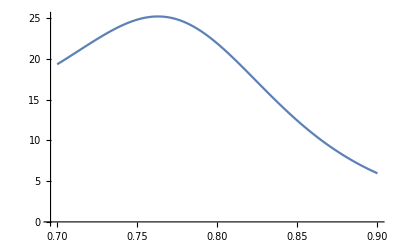

```mathematica
ListLinePlot[Table[{g11[[101+201 i,1]],g11[[101+201 i,3]]},{i,0,200}]]
```

```mathematica
Clear[g11]
```